## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=10;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=MachinePrecision,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071569794667184382685327194155911419117565041803) 小于 WorkingPrecision (50.).

-0.000715697824472766851188234094351789823890686276733

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.23022275482424902039019236522113846033884943201) 小于 WorkingPrecision (50.).

-0.2262799408311053437521602062160850541636342005515

NDSolve::precw: The precision of the differential equation ({{20 (0.003+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0922532) is less than WorkingPrecision (50.).

{0.01,0.091992793291971523560774366797581782979523942284869}    1.593752

NDSolve::precw: The precision of the differential equation ({{20 (0.03+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500215) is less than WorkingPrecision (50.).

{0.003,-0.46381938738580464655341294116408889626239636377145}    1.718756

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022275482424902039019236522113846033884943201) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.007+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.2262799408311053437521602062160850541636342005515}    1.750004

NDSolve::precw: The precision of the differential equation ({{20 (0.001+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.20307) is less than WorkingPrecision (50.).

{0.07,-0.87731521355405218586981611414275997028076278607672}    1.875005

NDSolve::precw: The precision of the differential equation ({{20 (0.1+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471268) is less than WorkingPrecision (50.).

{0.03,0.44039857041011956438201798589988324278269394313205}    1.718767

NDSolve::precw: The precision of the differential equation ({{20 (0.3+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30367) is less than WorkingPrecision (50.).

{0.001,0.91646147946676308567436682849950263045022845411366}    1.671891

NDSolve::precw: The precision of the differential equation ({{20 (0.7+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386214) is less than WorkingPrecision (50.).

{0.007,0.36856573102412516393305178457286993464640585631532}    1.843765

FindRoot::precw: The precision of the argument function (Tan[δ]==0.192248) is less than WorkingPrecision (50.).

{0.1,0.18993104896119526995415287091261848530315457291741}    2.375022

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.376669) is less than WorkingPrecision (50.).

{0.3,-0.36023345558259243717184476411541729054492945744525}    2.484395

FindRoot::precw: The precision of the argument function (Tan[δ]==2.28292) is less than WorkingPrecision (50.).

{0.7,1.1579370160845887554630339814969069502397964365251}    3.765661

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.81087942743321473041416645527235780198478045675) is less than WorkingPrecision (50.).

{1,-0.68133962370253816118007308447789488292714420092942}    3.76566

{-0.2262799408311053437521602062160850541636342005515,0.91646147946676308567436682849950263045022845411366,-0.46381938738580464655341294116408889626239636377145,0.36856573102412516393305178457286993464640585631532,0.091992793291971523560774366797581782979523942284869,0.44039857041011956438201798589988324278269394313205,-0.87731521355405218586981611414275997028076278607672,0.18993104896119526995415287091261848530315457291741,-0.36023345558259243717184476411541729054492945744525,1.1579370160845887554630339814969069502397964365251,-0.68133962370253816118007308447789488292714420092942}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={10,5,1,0.1,0.05,0.01,0.005,0.003};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{c1start_,c1end_}]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,c1start,c1end},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
Determinec1[aa[[8]],{-6.6,-6.4}]
```

0.003

Run

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+139.686 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071569510271125483394002199682476413827072217784) 小于 WorkingPrecision (50.).

End with 33.6306686s

Run

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+135.453 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071569929759664961356778509868893372640963464329) 小于 WorkingPrecision (50.).

End with 37.0809947s

Run

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+135.453 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00071569929759664961356778509868893372640963464329) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

End with 36.1827712s

{-6.4,-1.3509241×10^-9}

Run

End with 44.9107669s

Run

End with 39.9682479s

{-6.46441,-5.1178133×10^-13}

Run

End with 27.2399526s

Run

End with 26.1848807s

{-6.46443,3.3297949×10^-20}

Run

End with 37.5053078s

Run

End with 37.7904004s

{-6.46443,1.4735106×10^-23}

Run

End with 37.7341136s

Run

End with 38.3917448s

{-6.46443,1.4735106×10^-23}

Run

End with 34.1878358s

Run

End with 38.3077387s

{-6.46443,1.4735106×10^-23}

Run

End with 49.6909569s

Run

End with 49.7070618s

Run

End with 37.6125508s

Run

End with 52.2160896s

Run

End with 39.4607388s

Run

End with 38.5615732s

{-6.4644325916917972918440682406071573495864868164063,1.4735106×10^-23}

Run

End with 36.7497587s

Run

End with 36.6230529s

{-6.4644325916917970662256347276017027283471785249471,1.4735106×10^-23}

Run

End with 47.9478014s

Run

End with 47.5492120s

{-6.4644325916917970662256347276017027283471785249471,1.4735106×10^-23}

Run

End with 41.0024538s

Run

End with 38.0291160s

{-6.4644325916917969820726408717009846492133414542026,1.4735106×10^-23}

Run

End with 37.7387569s

Run

End with 40.4845370s

{-6.4644325916917968585091412528713992593637534442756,1.4735106×10^-23}

Run

End with 53.2944444s

Run

End with 40.6713484s

{-6.4644325916917968585091412528713992593637534442756,1.4735106×10^-23}

Run

End with 52.9786401s

Run

End with 40.5166430s

{-6.4644325916917968585091412528713992593637534442756,1.4735106×10^-23}

Run

End with 40.3195297s

Run

End with 40.4297163s

{-6.4644325916917968545224837199726265049956444061706,1.4735106×10^-23}

Run

End with 40.6949392s

Run

End with 41.0803965s

{-6.4644325916917968486687958833847349755286952699285,1.4735106×10^-23}

Run

End with 51.6294139s

Run

End with 39.6156516s

{-6.4644325916917968486687958833847349755286952699285,1.4735106×10^-23}

Run

End with 39.8425973s

Run

End with 54.1470882s

{-6.4644325916917968479253079474748529905827528319008,1.4735106×10^-23}

Run

End with 76.4040863s

Run

End with 58.5631509s

{-6.4644325916917968479253079474748529905827528319008,1.4735106×10^-23}

Run

End with 82.6979371s

Run

End with 63.0816220s

{-6.4644325916917968479253079474748529905827528319008,1.4735106×10^-23}

Run

End with 61.7967425s

Run

End with 60.2966577s

{-6.4644325916917968478548640655758929277431048390015,1.4735106×10^-23}

Run

End with 76.3764746s

Run

End with 55.4213591s

{-6.4644325916917968478548640655758929277431048390015,1.4735106×10^-23}

Run

End with 55.9122559s

Run

End with 58.3240502s

{-6.4644325916917968478285893349684433943235511519258,1.4735106×10^-23}

Run

End with 55.7679131s

Run

End with 54.6803271s

{-6.4644325916917968477900096301161389328897547140917,1.4735106×10^-23}

Run

End with 55.5296765s

Run

End with 55.8496061s

{-6.4644325916917968477707197776899867021728564951746,1.4735106×10^-23}

Run

End with 55.8862766s

Run

End with 58.9763800s

{-6.4644325916917968477610748514769105868144073857161,1.4735106×10^-23}

Run

End with 62.2601922s

Run

End with 45.5713166s

{-6.4644325916917968477562523883703725291351828309868,1.4735106×10^-23}

Run

End with 80.7218325s

Run

End with 52.0988300s

{-6.4644325916917968477562523883703725291351828309868,1.4735106×10^-23}

Run

End with 38.8812991s

Run

End with 43.7773100s

{-6.4644325916917968477556398782329731476139005528192,1.4735106×10^-23}

Run

End with 82.0219487s

Run

End with 60.3904064s

{-6.4644325916917968477556398782329731476139005528192,1.4735106×10^-23}

Run

End with 58.3331791s

Run

End with 56.4486158s

{-6.4644325916917968477554114192324089235713157310494,1.4735106×10^-23}

Run

End with 55.2261726s

Run

End with 55.2084386s

{-6.464432591691796847755075968378723623763025642135,1.4735106×10^-23}

Run

End with 55.7723006s

Run

End with 55.0541149s

{-6.4644325916917968477549082429518809738588805976779,1.4735106×10^-23}

Run

End with 75.3432313s

Run

End with 57.7179344s

{-6.4644325916917968477549082429518809738588805976779,1.4735106×10^-23}

Run

End with 58.7643068s

Run

End with 57.3443968s

{-6.4644325916917968477548869398289806699954687119802,1.4735106×10^-23}

Run

End with 77.0163779s

Run

End with 58.6696126s

{-6.4644325916917968477548869398289806699954687119802,1.4735106×10^-23}

Run

End with 59.7385401s

Run

End with 61.0134080s

{-6.4644325916917968477548789940173613484296586759508,1.4735106×10^-23}

Run

End with 56.9891378s

Run

End with 55.6345762s

{-6.4644325916917968477548673270255407539403985348328,1.4735106×10^-23}

Run

End with 55.9016647s

Run

End with 56.5034192s

{-6.4644325916917968477548614935296304566957684642738,1.4735106×10^-23}

Run

End with 56.4973580s

Run

End with 57.1057814s

{-6.4644325916917968477548585767816753080734534289943,1.4735106×10^-23}

Run

End with 80.2818386s

Run

End with 63.8469174s

{-6.4644325916917968477548585767816753080734534289943,1.4735106×10^-23}

Run

End with 81.7044228s

Run

End with 61.1677559s

{-6.4644325916917968477548585767816753080734534289943,1.4735106×10^-23}

Run

End with 70.7031375s

Run

End with 69.1469248s

{-6.4644325916917968477548584826756064217858667239983,1.4735106×10^-23}

Run

End with 85.0813113s

Run

End with 132.7736406s

{-6.4644325916917968477548584826756064217858667239983,1.4735106×10^-23}

Run

End with 105.6045520s

Run

End with 69.5301705s

{-6.4644325916917968477548584475751613318937246905394,1.4735106×10^-23}

Run

End with 83.8349434s

Run

End with 83.5056317s

{-6.4644325916917968477548583960364859413030750082117,1.4735106×10^-23}

Run

End with 111.9464232s

Run

End with 84.6014183s

{-6.4644325916917968477548583960364859413030750082117,1.4735106×10^-23}

Run

End with 122.6382325s

Run

End with 90.7248722s

{-6.4644325916917968477548583960364859413030750082117,1.4735106×10^-23}

Run

End with 102.1762165s

Run

End with 100.8695693s

{-6.464432591691796847754858394373640124250705641524,1.4735106×10^-23}

Run

End with 101.6870744s

Run

End with 101.2620786s

{-6.4644325916917968477548583919320508347079702268946,1.4735106×10^-23}

Run

End with 99.8365618s

Run

End with 100.2623688s

{-6.4644325916917968477548583907112561899366025195799,1.4735106×10^-23}

Run

End with 130.2983811s

Run

End with 99.6195272s

{-6.4644325916917968477548583907112561899366025195799,1.4735106×10^-23}

Run

End with 97.6465234s

Run

End with 99.9466971s

{-6.4644325916917968477548583905562007589076790968289,1.4735106×10^-23}

Run

End with 127.9644660s

Run

End with 97.3324610s

{-6.4644325916917968477548583905562007589076790968289,1.4735106×10^-23}

Run

End with 125.9102028s

Run

End with 96.8968855s

{-6.4644325916917968477548583905562007589076790968289,1.4735106×10^-23}

Run

End with 122.6691146s

Run

End with 80.6322602s

{-6.4644325916917968477548583905562007589076790968289,1.4735106×10^-23}

Run

End with 98.8140154s

Run

End with 101.3211743s

{-6.4644325916917968477548583905524688528764341292933,1.4735106×10^-23}

Run

End with 96.8223561s

Run

End with 90.2910098s

{-6.4644325916917968477548583905469892216911330300139,1.4735106×10^-23}

Run

End with 132.1701642s

Run

End with 97.1399521s

{-6.4644325916917968477548583905469892216911330300139,1.4735106×10^-23}

Run

End with 95.0598167s

Run

End with 94.1711281s

{-6.4644325916917968477548583905462932433962122527229,1.4735106×10^-23}

Run

End with 91.0426431s

Run

End with 90.3603598s

{-6.4644325916917968477548583905452713247473473665486,1.4735106×10^-23}

Run

End with 91.4781238s

Run

End with 91.2728509s

{-6.4644325916917968477548583905447603654229149234614,1.4735106×10^-23}

Run

End with 118.3498719s

Run

End with 91.0549849s

{-6.4644325916917968477548583905447603654229149234614,1.4735106×10^-23}

Run

End with 90.2165268s

Run

End with 90.3288039s

{-6.4644325916917968477548583905446954675151239225078,1.4735106×10^-23}

Run

End with 90.3884633s

Run

End with 88.0083098s

{-6.4644325916917968477548583905446001766379113122128,1.4735106×10^-23}

Run

End with 93.0472473s

Run

End with 89.2667744s

{-6.4644325916917968477548583905445525311993050070653,1.4735106×10^-23}

Run

End with 116.9095619s

Run

End with 90.9774602s

{-6.4644325916917968477548583905445525311993050070653,1.4735106×10^-23}

Run

End with 89.0141881s

Run

End with 92.0253291s

{-6.4644325916917968477548583905445464796622579664224,1.4735106×10^-23}

Run

End with 120.6437966s

Run

End with 89.2608700s

{-6.4644325916917968477548583905445464796622579664224,1.4735106×10^-23}

Run

End with 98.2263249s

Run

End with 95.0994106s

{-6.4644325916917968477548583905445442225108718452547,1.4735106×10^-23}

Run

End with 116.3266839s

Run

End with 97.1288570s

{-6.4644325916917968477548583905445442225108718452547,1.4735106×10^-23}

Run

End with 101.5944920s

Run

End with 91.9703614s

{-6.4644325916917968477548583905445433806202347615465,1.4735106×10^-23}

Run

End with 102.6406735s

Run

End with 87.1059633s

{-6.4644325916917968477548583905445421444556178197011,1.4735106×10^-23}

Run

End with 91.3003661s

Run

End with 100.7825659s

{-6.4644325916917968477548583905445415263733093487785,1.4735106×10^-23}

Run

End with 101.6643067s

Run

End with 104.5139662s

{-6.4644325916917968477548583905445412173321551133172,1.4735106×10^-23}

Run

End with 133.7561013s

Run

End with 101.3385560s

{-6.4644325916917968477548583905445412173321551133172,1.4735106×10^-23}

Run

End with 132.6470133s

Run

End with 101.6813255s

{-6.4644325916917968477548583905445412173321551133172,1.4735106×10^-23}

Run

End with 107.6247695s

Run

End with 104.5324794s

{-6.4644325916917968477548583905445412073612393549488,1.4735106×10^-23}

Run

End with 99.9685734s

Run

End with 97.9913013s

{-6.464432591691796847754858390544541192720747210151,1.4735106×10^-23}

Run

End with 97.8099440s

Run

End with 99.3490122s

{-6.464432591691796847754858390544541185400501137752,1.4735106×10^-23}

Run

End with 100.0416923s

Run

End with 100.8081010s

{-6.4644325916917968477548583905445411817403781015526,1.4735106×10^-23}

Run

End with 121.1453344s

Run

End with 101.0809080s

{-6.4644325916917968477548583905445411817403781015526,1.4735106×10^-23}

Run

End with 99.2616176s

Run

End with 96.5405622s

{-6.4644325916917968477548583905445411812754989694009,1.4735106×10^-23}

Run

End with 101.2018493s

Run

End with 100.2904256s

{-6.4644325916917968477548583905445411805929077764269,1.4735106×10^-23}

Run

End with 94.0477613s

Run

End with 73.5108078s

{-6.4644325916917968477548583905445411802516121799399,1.4735106×10^-23}

Run

End with 120.0623739s

Run

End with 73.0278987s

{-6.4644325916917968477548583905445411802516121799399,1.4735106×10^-23}

Run

End with 63.9951280s

Run

End with 67.6617580s

{-6.4644325916917968477548583905445411802082635823291,1.4735106×10^-23}

Run

End with 87.0664905s

Run

End with 65.5891631s

{-6.4644325916917968477548583905445411801446139820127,1.4735106×10^-23}

Run

End with 78.4650335s

Run

End with 62.0734690s

{-6.4644325916917968477548583905445411801446139820127,1.4735106×10^-23}

Run

End with 55.1273389s

Run

End with 54.9905439s

{-6.4644325916917968477548583905445411801365297261929,1.4735106×10^-23}

Run

End with 70.9532581s

Run

End with 54.9477666s

{-6.4644325916917968477548583905445411801365297261929,1.4735106×10^-23}

Run

End with 72.2808381s

Run

End with 55.9661653s

{-6.4644325916917968477548583905445411801365297261929,1.4735106×10^-23}

Run

End with 55.4696694s

Run

End with 55.5724970s

{-6.4644325916917968477548583905445411801357637603517,1.4735106×10^-23}

Run

End with 54.6454454s

Run

End with 57.5735636s

{-6.4644325916917968477548583905445411801346390776092,1.4735106×10^-23}

Run

End with 61.9639101s

Run

End with 57.4647876s

{-6.4644325916917968477548583905445411801340767362379,1.4735106×10^-23}

Run

End with 79.9389197s

Run

End with 56.2957450s

{-6.4644325916917968477548583905445411801340767362379,1.4735106×10^-23}

Run

End with 59.5213556s

Run

End with 57.7945124s

{-6.4644325916917968477548583905445411801340053121994,1.4735106×10^-23}

Run

End with 54.5946209s

Run

End with 54.3776426s

{-6.4644325916917968477548583905445411801339004388758,1.4735106×10^-23}

Run

End with 54.3164612s

Run

End with 54.8307143s

{-6.4644325916917968477548583905445411801338480022141,1.4735106×10^-23}

Run

End with 54.4367141s

Run

End with 54.2744862s

{-6.4644325916917968477548583905445411801338217838832,1.4735106×10^-23}

Run

End with 71.9543793s

Run

End with 55.4975808s

{-6.4644325916917968477548583905445411801338217838832,1.4735106×10^-23}

Run

End with 72.7300418s

Run

End with 55.6445233s

{-6.4644325916917968477548583905445411801338217838832,1.4735106×10^-23}

Run

End with 55.4369596s

Run

End with 55.3276150s

{-6.4644325916917968477548583905445411801338209379739,1.4735106×10^-23}

Run

End with 55.2484078s

Run

End with 55.2836454s

{-6.4644325916917968477548583905445411801338196959087,1.4735106×10^-23}

Run

End with 71.2427870s

Run

End with 53.6176156s

{-6.4644325916917968477548583905445411801338196959087,1.4735106×10^-23}

Run

End with 66.8983187s

Run

End with 37.1338436s

{-6.4644325916917968477548583905445411801338196959087,1.4735106×10^-23}

Run

End with 37.9338235s

Run

End with 41.8041221s

{-6.4644325916917968477548583905445411801338196558347,1.4735106×10^-23}

Run

End with 39.9713393s

Run

End with 37.5186867s

{-6.4644325916917968477548583905445411801338195969932,1.4735106×10^-23}

Run

End with 48.3964661s

Run

End with 37.1229136s

{-6.4644325916917968477548583905445411801338195969932,1.4735106×10^-23}

Run

End with 37.1355953s

Run

End with 37.1784055s

{-6.4644325916917968477548583905445411801338195895196,1.4735106×10^-23}

Run

End with 48.1667058s

Run

End with 37.1900683s

{-6.4644325916917968477548583905445411801338195895196,1.4735106×10^-23}

Run

End with 37.1336842s

Run

End with 37.3397117s

{-6.4644325916917968477548583905445411801338195867321,1.4735106×10^-23}

Run

End with 37.5952503s

Run

End with 37.1334728s

{-6.464432591691796847754858390544541180133819582639,1.4735106×10^-23}

Run

End with 37.0645876s

Run

End with 37.0724467s

{-6.4644325916917968477548583905445411801338195805925,1.4735106×10^-23}

Run

End with 48.1243985s

Run

End with 37.0405682s

{-6.4644325916917968477548583905445411801338195805925,1.4735106×10^-23}

Run

End with 37.3790080s

Run

End with 36.8991385s

{-6.4644325916917968477548583905445411801338195803326,1.4735106×10^-23}

Run

End with 48.1801175s

Run

End with 37.0905186s

{-6.4644325916917968477548583905445411801338195803326,1.4735106×10^-23}

Run

End with 37.0654013s

Run

End with 37.2183874s

{-6.4644325916917968477548583905445411801338195802356,1.4735106×10^-23}

Run

End with 37.0098848s

Run

End with 36.9946880s

{-6.4644325916917968477548583905445411801338195800933,1.4735106×10^-23}

Run

End with 48.3170471s

Run

End with 37.0266806s

{-6.4644325916917968477548583905445411801338195800933,1.4735106×10^-23}

Run

End with 48.1439623s

Run

End with 36.9683866s

{-6.4644325916917968477548583905445411801338195800933,1.4735106×10^-23}

Run

End with 37.0736656s

Run

End with 37.0079240s

{-6.4644325916917968477548583905445411801338195800887,1.4735106×10^-23}

Run

End with 36.9150316s

Run

End with 37.1673794s

{-6.4644325916917968477548583905445411801338195800819,1.4735106×10^-23}

Run

End with 37.5668121s

Run

End with 36.9760643s

{-6.4644325916917968477548583905445411801338195800786,1.4735106×10^-23}

Run

End with 48.2065025s

Run

End with 37.0839059s

{-6.4644325916917968477548583905445411801338195800786,1.4735106×10^-23}

Run

End with 37.0395479s

Run

End with 37.1035062s

{-6.4644325916917968477548583905445411801338195800781,1.4735106×10^-23}

Run

End with 50.3317541s

Run

End with 37.6428844s

{-6.4644325916917968477548583905445411801338195800781,1.4735106×10^-23}

Run

End with 48.0869871s

FindRoot::brdig: 根已经被 50. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-25.

-6.4644325916917968477548583905445411801338195800781

-6.4644325916917968477548583905445411801338195800781

```mathematica
AppendTo[c1a,%]
```

{-5.8715165083209699914791986973746085778041560240936,2.6057556866316062549793203766021593828446947443544,6.8723581237385142564773830019844494032690878395545,-17.413010990120400585282775903011638274197195074326,-10.664149237196414610195915884105488657951354980469,-6.9202747389080444150377016687762690561842616868644,-6.5898375844119612132487873168429359793663024902347,-6.4644325916917968477548583905445411801338195800781}

```mathematica
c1a=Determinec1[#]&/@Drop[aa,0];
```

10

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+0.0190481 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00066953931571743403499937883257453868512578550189) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{20 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00073621859476001364957478755930777747723609645656) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{20 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00073621859476001364957478755930777747723609645656) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{0.,-0.000020520637}

{-0.923254,1.8168436×10^-6}

{-0.848161,5.8027791×10^-7}

{-0.813891,3.7820825×10^-10}

{-0.813868,-3.1050339×10^-14}

{-0.8138684750227651587550781187019,1.8765628×10^-19}

{-0.813868475022754170227910893458,2.7983971×10^-25}

{-0.81386847502275417021152438675556874659969773442972,-2.2749416×10^-25}

{-0.81386847502275417021152438675556874659969773442972,-2.2749416×10^-25}

{-0.81386847502275417021152438675556874659969773442972,-2.2749416×10^-25}

«3 more identical outputs»

-0.81386847502275417021152471209700361576249188557557

5

{-3.,-0.000015928379}

{0.,0.000038606321}

{-2.12377,-0.000053581567}

{-0.889388,0.00010760581}

{-1.71344,-0.00013158374}

{-1.61144,-0.00019120464}

{-1.26011,0.00045325824}

{-1.43578,-0.0007184754}

{-1.32806,0.0011926947}

{-1.39528,-0.0018391656}

{-1.3545,0.0033515935}

{-1.38083,-0.004097829}

{-1.37817,-0.0052911536}

{-1.37226,-0.014943477}

{-1.36635,0.018205267}

{-1.36664,0.020442408}

{-1.36797,0.046523475}

{-1.36864,0.12818583}

{-1.36931,-0.16609262}

{-1.36925,-0.20407328}

{-1.36911,-0.4702426}

{-1.36897,0.83967124}

{-1.36904,-1.0793577}

{-1.369,1.3068068}

{-1.36903,-1.4015702}

{-1.36902,-1.5097807}

{-1.36901,1.5134222}

{-1.369015534224610863844873165363,1.5424649}

{-1.36901626607373905208930864319,1.5575412}

{-1.369016631998303146211526382103,1.565082}

{-1.36901681496058519327263525156,1.5688527}

{-1.369016997922867240333744121017,-1.5689692}

{-1.369016952208066763845144873216,-1.5699113}

{-1.369016952208066763845144873216,-1.5699113}

$Aborted

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-200,-500},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a[[7]]=%
```

```mathematica
AppendTo[c1a,%]
```

```mathematica
c1a
```

{-2.8099556213842111234426019073166335782646296855965,0.06710830044399914552351467211288260501415476966558,-1.7413010994999276045021637684668162317711110996265,-0.6920274738976314732319394806836498901247978210449,-0.65898375844282569557819329020276200026273727416991,-0.6342706750303552243330784676800249144434928894043,-0.63128358064966533236272994145110715180635452270509,-0.63009492577769449228597409273788798600435256958012}

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)-1}];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=δa~Join~Evaluate[δ50[Vs1[r,aa[[8]],c1a[[8]]]]]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({Drop[ee,1]}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.32945) is less than WorkingPrecision (50.).

End with 3.3481172s

{0.01,0.92589294596500592340984167727519361686172397498457}    3.348117

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022121181544731849250944287387438355960255787) is less than WorkingPrecision (50.).

End with 3.4782736s

{1/100000,-0.22627847548862271137093134964259335947339939545242}    3.492284

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.446822) is less than WorkingPrecision (50.).

End with 3.8713786s

{0.003,-0.4202076449618921646227588192493921391799608167101}    3.887005

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0414748) is less than WorkingPrecision (50.).

End with 4.3088821s

{0.07,0.041451050282009014874716474246638123880957122749171}    4.324509

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.772124) is less than WorkingPrecision (50.).

End with 3.4569749s

{0.03,0.65751049057968091259706541853129936282518892206354}    3.456975

Run

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30711) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 3.4140059s

{0.001,0.91773556844516592970393550602147984289934506313475}    3.429631

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.037280393156121740833183513659958688428711507821284 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.40952) is less than WorkingPrecision (50.).

End with 4.2113523s

{0.007,0.38868663736404091311043641050282304875547042380954}    4.226978

Run

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.632679) is less than WorkingPrecision (50.).

End with 5.2446217s

{0.1,-0.56410236928185518917312186211781889600520697255261}    5.260248

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.656026) is less than WorkingPrecision (50.).

End with 7.5281842s

{0.3,-0.58059943741956481136507375787494221095677307515725}    7.5438113

FindRoot::precw: The precision of the argument function (Tan[δ]==0.317466) is less than WorkingPrecision (50.).

End with 12.7344412s

{0.7,0.3074030119729961013374753765609196407863684373182}    12.781314

FindRoot::precw: The precision of the argument function (Tan[δ]==-20.9546135539980660013787824098419005705360101) is less than WorkingPrecision (50.).

End with 13.9206832s

{1,-1.52311031734756493375778375525501348662832278255}    13.951932

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (0.003-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022103849842810679498094570425731960994791933) is less than WorkingPrecision (50.).

End with 3.9024266s

{1/100000,-0.22627831089533832120885068379409129568386011983082}    3.902427

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.440454) is less than WorkingPrecision (50.).

End with 4.5743091s

{0.003,-0.41488718785223465480950322972016148062446938563917}    4.589935

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.60363) is less than WorkingPrecision (50.).

End with 4.8086869s

{0.01,1.0132163570600943930313248722292977256648681952038}    4.808687

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0570801) is less than WorkingPrecision (50.).

End with 4.9024360s

{0.07,0.057018265573588174603773028807504262204575884609044}    4.918062

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30749) is less than WorkingPrecision (50.).

End with 4.3356563s

{0.001,0.9178763841420889235422479985195198623525349319895}    4.351279

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.812379) is less than WorkingPrecision (50.).

End with 3.9294004s

{0.03,0.68224364837858377672083736467890451797711077905047}    3.945026

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.7-0.033089780580113061344170654879650815570758821209866 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.411865) is less than WorkingPrecision (50.).

End with 4.3512789s

{0.007,0.39069278875341971815409960574915687932678384456959}    4.366916

Run

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.602843) is less than WorkingPrecision (50.).

End with 4.6258426s

{0.1,-0.54250755412147963227954963301960167938298452521672}    4.64147

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.588211) is less than WorkingPrecision (50.).

End with 9.1857719s

{0.3,-0.53170567515083426465390156971911454425855302344281}    9.2170211

FindRoot::precw: The precision of the argument function (Tan[δ]==0.337988) is less than WorkingPrecision (50.).

End with 12.6874550s

{0.7,0.32593421328120236657966521002286865949615348756572}    12.718707

FindRoot::precw: The precision of the argument function (Tan[δ]==-16.67838167821415675004196160580911544028295792) is less than WorkingPrecision (50.).

End with 15.9243609s

{1,-1.51091016502202724776351412177864027385920448961}    15.955627

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (0.003-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.492387) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022250832511794404501664495988862246504091353) is less than WorkingPrecision (50.).

End with 3.0200725s

End with 3.0356995s

{0.003,-0.45753901374237342722052943845058312223694942198739}    3.0357

{1/100000,-0.22627970673941000671591097247270202360887893299204}    3.051324

Run

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.001-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.545864) is less than WorkingPrecision (50.).

End with 3.9985705s

{0.07,-0.49966217545387818443630895090757313081492493134696}    4.014195

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.196439) is less than WorkingPrecision (50.).

End with 4.3110741s

{0.01,0.19396913658844081606095951613788854466391281164048}    4.326699

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30422) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.389924) is less than WorkingPrecision (50.).

End with 3.2777713s

End with 3.2933959s

{0.001,0.91666474401409616633483674887032396679758183862846}    3.293392

{0.007,0.37178997347498506674200199722931796926940849701661}    3.309017

Run

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.7-0.43635100471837657787960963567811896851720648215908 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.503752) is less than WorkingPrecision (50.).

End with 3.7100637s

{0.03,0.46664473479141103374811565386733583538494286351574}    3.710064

Run

FindRoot::precw: The precision of the argument function (Tan[δ]==0.7761) is less than WorkingPrecision (50.).

End with 5.0850780s

{0.1,0.65999711100857048751332958092751055274419387941324}    5.100703

FindRoot::precw: The precision of the argument function (Tan[δ]==3.85935) is less than WorkingPrecision (50.).

End with 5.8745558s

{0.3,1.317261127545584836122439271233037379013658979533}    5.890178

FindRoot::precw: The precision of the argument function (Tan[δ]==0.240874) is less than WorkingPrecision (50.).

End with 8.4565837s

{0.7,0.23637158182436341117289420361651689486084803837698}    8.4878464

FindRoot::precw: The precision of the argument function (Tan[δ]==7.983651882111913272164761654149013291915955916) is less than WorkingPrecision (50.).

End with 8.7846359s

{1,1.446189315670970720653059445623177433655484065135}    8.815883

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.091552) is less than WorkingPrecision (50.).

End with 2.7548958s

{0.01,0.091297477820837066347910520832177401576411784159884}    2.754896

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022275661702959025190199510652281431753486735) is less than WorkingPrecision (50.).

End with 2.9521922s

{1/100000,-0.22627994253364692412840292151857728988211954170293}    2.971206

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.21268) is less than WorkingPrecision (50.).

Run

End with 3.0125623s

NDSolve::precw: The precision of the differential equation ({{20 (0.001+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.07,-0.88122067453802999840598288879426319860215931588797}    3.028187

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500271) is less than WorkingPrecision (50.).

End with 3.1688134s

Run

{0.003,-0.463864325354229156355723851832172144497844947927}    3.184441

NDSolve::precw: The precision of the differential equation ({{20 (0.1+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30366) is less than WorkingPrecision (50.).

End with 2.7665090s

{0.001,0.91646000033782823428949163261579779616346818210132}    2.782634

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471037) is less than WorkingPrecision (50.).

End with 3.2176969s

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386187) is less than WorkingPrecision (50.).

{0.03,0.44021008413009098554685371794864271536746717054137}    3.233321

End with 2.8194034s

{0.007,0.36854212347704021512074835410999367212247934232849}    2.835028

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.7+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

Run

NDSolve::precw: The precision of the differential equation ({{20 (1+11.0562 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.189714) is less than WorkingPrecision (50.).

End with 3.0850333s

{0.1,0.18748630428332936987237590922063100771812869948383}    3.10066

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.386687) is less than WorkingPrecision (50.).

End with 4.0218752s

{0.3,-0.36897722554205438637355980102318878015262218862376}    4.053126

FindRoot::precw: The precision of the argument function (Tan[δ]==2.17808) is less than WorkingPrecision (50.).

End with 5.8711409s

{0.7,1.140384871016621795822986926313883014331116591581}    5.902382

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.87766866720185230422470804715157925944843633764) is less than WorkingPrecision (50.).

End with 6.1752619s

{1,-0.72033945970473213841638253142805924769707965194816}    6.206496

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0919219) is less than WorkingPrecision (50.).

End with 2.5479024s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022275567044142140748585894588393457610761672) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500241) is less than WorkingPrecision (50.).

{0.01,0.091664285633340361896970267172964141029288646313808}    2.563526

End with 2.5947770s

End with 2.5947770s

Run

{1/100000,-0.22627994163470494330585153470574307142022054041993}    2.610402

{0.003,-0.46384060399534818599543925346202840860825293436486}    2.610402

NDSolve::precw: The precision of the differential equation ({{20 (0.03+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

Run

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.007+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.20761) is less than WorkingPrecision (50.).

End with 2.9621316s

{0.07,-0.87916531522843301749351042930373772381432026748935}    2.99338

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30367) is less than WorkingPrecision (50.).

End with 2.5125026s

{0.001,0.91646078126942443731648481717902676535236372416172}    2.528127

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386201) is less than WorkingPrecision (50.).

End with 2.5906292s

Run

{0.007,0.36855458292784080931898655001635581644451139031675}    2.590629

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471159) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 2.7468803s

Run

{0.03,0.44030940888022006536780341896993215535573353359148}    2.762505

NDSolve::precw: The precision of the differential equation ({{20 (0.7+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

Run

NDSolve::precw: The precision of the differential equation ({{20 (1+13.5421 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.191042) is less than WorkingPrecision (50.).

End with 3.2571105s

{0.1,0.1887674517097607743213286919674580269741592215697}    3.272734

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.381507) is less than WorkingPrecision (50.).

End with 3.8579472s

{0.3,-0.36446359743561605151535152824455987788750214954525}    3.889199

FindRoot::precw: The precision of the argument function (Tan[δ]==2.22961) is less than WorkingPrecision (50.).

End with 5.8165974s

{0.7,1.1491824456040140854022221513322248043411324092319}    5.863472

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.8443853104424333697969242139740545279703380745) is less than WorkingPrecision (50.).

End with 6.6134790s

{1,-0.70122540287646570451968519274062786092554167594584}    6.644741

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0922515) is less than WorkingPrecision (50.).

End with 5.1728639s

{0.01,0.091991165791786099144671635276771565706220002650309}    5.204115

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.20309) is less than WorkingPrecision (50.).

End with 6.9354731s

{0.07,-0.87732438909047222220277694562412500890645539570477}    6.951088

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500215) is less than WorkingPrecision (50.).

End with 7.1385886s

{0.003,-0.4638194924489590054829033680040172031422988209493}    7.1698374

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.2302227548284385465684713806798761481323162879) is less than WorkingPrecision (50.).

Run

End with 7.2323381s

NDSolve::precw: The precision of the differential equation ({{20 (0.007+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.22627994083508399158184651673731484993476020346036}    7.2479636

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471267) is less than WorkingPrecision (50.).

End with 5.2626612s

{0.03,0.44039812839390407306772828476472662754827662971703}    5.293913

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30367) is less than WorkingPrecision (50.).

End with 6.2922184s

{0.001,0.91646147600982708491328934665275772217951651460855}    6.323469

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386214) is less than WorkingPrecision (50.).

End with 6.4640950s

Run

{0.007,0.36856567581452556385767802041269549394084906971054}    6.495345

NDSolve::precw: The precision of the differential equation ({{20 (0.7+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

Run

NDSolve::precw: The precision of the differential equation ({{20 (1+43.9393 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.192242) is less than WorkingPrecision (50.).

End with 6.8234896s

{0.1,0.18992525744759828388332711880007093992732960940877}    6.839099

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.376694) is less than WorkingPrecision (50.).

End with 11.3376557s

{0.3,-0.3602547331197963782890003010849037292224666090477}    11.368907

FindRoot::precw: The precision of the argument function (Tan[δ]==2.28264) is less than WorkingPrecision (50.).

End with 15.6896038s

{0.7,1.1578920742828644795522357601216694782913482791712}    15.752093

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.81105128258099147709418557512057860800048218387) is less than WorkingPrecision (50.).

End with 17.8191978s

{1,-0.68144329674138084224851883777329378643866523290229}    17.850447

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022275482454593488623124013907153976920782635) is less than WorkingPrecision (50.).

End with 30.8433366s

{1/100000,-0.22627994083138731315991641808878643633645201151899}    30.891369

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0922531) is less than WorkingPrecision (50.).

End with 32.5146152s

{0.01,0.091992677948221068541262315579254326682713837888834}    32.545867

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.20307) is less than WorkingPrecision (50.).

End with 35.5633882s

{0.07,-0.87731586389033909110114147845687284213796731589546}    35.610266

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500215) is less than WorkingPrecision (50.).

End with 40.8767395s

{0.003,-0.46381939483173319049718280948757538434096853324154}    40.907984

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30367) is less than WorkingPrecision (50.).

End with 30.0687399s

{0.001,0.91646147922176736195613982557355405417461083374089}    30.101604

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471267) is less than WorkingPrecision (50.).

End with 31.1437093s

{0.03,0.44039853908281703752154755248711664776635532170935}    31.179537

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.7+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386214) is less than WorkingPrecision (50.).

End with 32.1035271s

{0.007,0.36856572711134626714230933957623741296678129755669}    32.134778

Run

NDSolve::precw: The precision of the differential equation ({{20 (1+83.6825 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.192248) is less than WorkingPrecision (50.).

End with 38.3434198s

{0.1,0.18993063845331650144251096050956307444645636977827}    38.374672

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.376671) is less than WorkingPrecision (50.).

End with 63.3671760s

{0.3,-0.36023496419148468330781156664192216541753320951658}    63.429678

FindRoot::precw: The precision of the argument function (Tan[δ]==2.2829) is less than WorkingPrecision (50.).

End with 91.6393020s

{0.7,1.1579338278040876333492147971423237314134768468708}    91.7018168

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.81089162359648338926062293285557906209915795744) is less than WorkingPrecision (50.).

End with 100.8783295s

{1,-0.68134698171356065963565193219117750610569001295543}    100.909567

Run

Run

Run

«1 more identical outputs»

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23022275482428945742651324076417114794403639876) is less than WorkingPrecision (50.).

End with 85.3886218s

{1/100000,-0.22627994083114374540426856768808253699921560680393}    85.4354959

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.001+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.500215) is less than WorkingPrecision (50.).

End with 86.3376031s

{0.003,-0.463819388399872955255335748594336329068069069843}    86.3688544

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.007+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0922532) is less than WorkingPrecision (50.).

End with 98.1687827s

{0.01,0.091992777583160596388174211734667195987904868257111}    98.2156577

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.03+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.20307) is less than WorkingPrecision (50.).

End with 108.5144252s

{0.07,-0.87731530212568132597782038339940923140413887256998}    108.56583

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.1+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.471268) is less than WorkingPrecision (50.).

End with 100.7290569s

{0.03,0.4403985661435901234316728020655396374706684474819}    100.775929

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.3+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.30367) is less than WorkingPrecision (50.).

End with 114.8642709s

{0.001,0.91646147943339685570128515544999847407182012159743}    114.895522

Run

NDSolve::precw: The precision of the differential equation ({{20 (0.7+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.386214) is less than WorkingPrecision (50.).

End with 114.3215417s

{0.007,0.36856573049123933456562233168455158526529888886345}    114.337166

Run

NDSolve::precw: The precision of the differential equation ({{20 (1+136.817 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.192248) is less than WorkingPrecision (50.).

End with 117.3023840s

{0.1,0.189930993052127610407190472094972168294721036618}    117.365383

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.37667) is less than WorkingPrecision (50.).

End with 217.3002947s

{0.3,-0.3602336610595063713898628603669345986350756951919}    217.362798

FindRoot::precw: The precision of the argument function (Tan[δ]==2.28292) is less than WorkingPrecision (50.).

End with 292.3817842s

{0.7,1.1579365817803540071329247750963695536528152794974}    292.428659

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.8108810889202026391031098790204511644189630594) is less than WorkingPrecision (50.).

End with 317.6581214s

{1,-0.68134062609175734278389094019527321637408684270086}    317.704996

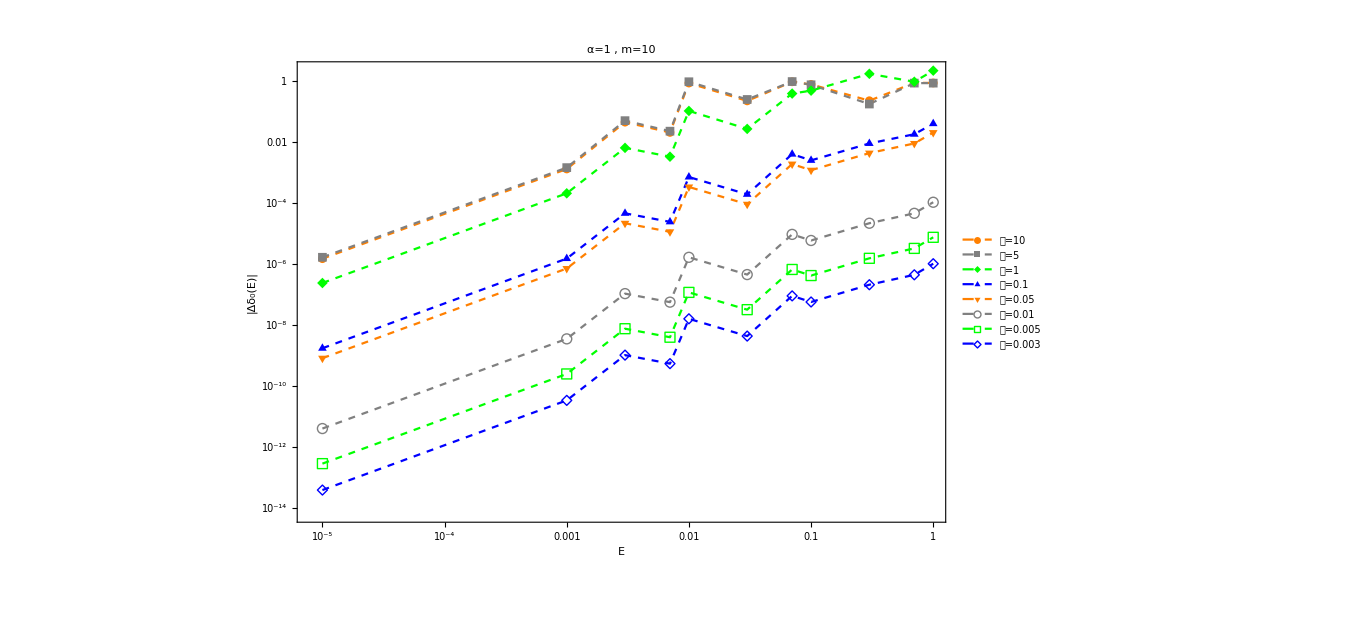

```mathematica
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa),PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),20]]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_Coulomb_5_Various_a_2.eps",%];
```

```mathematica
a=;
```

## Calculating eigenenergy of Coulomb Potential

```mathematica
EigenEnergy[V[r],αSch]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc[c1_]:=N[hhhc[10^-10,c1]-δ50e[10^-10,V[r]],8];
Determinec1:=Module[{aaa,findroot},aaa=a;
Print[a];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-40},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1
```

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch]
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,c2,d1]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δ50e[ee[[1]],V[r]],8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δ50e[ee[[2]],V[r]],8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δ50e[ee[[1]],V[r]],hhh[ee[[2]],c2,d1]==δ50e[ee[[2]],V[r]]},{{c2,-40.},{d1,3.}},MaxIterations->10000,AccuracyGoal->12,WorkingPrecision->50,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
```

## Matrix element <p^4>

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,b},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

```mathematica
efVs1=Module[{ef,am},
ef=Eigenfun[Vs1[r,a,c1],energyVs1];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs1=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

### Matrix element in V_eff^(a^4)

```mathematica
efVs2=Module[{ef,am},
ef=Eigenfun[Vs2[r,a,c1],energyVs2];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```